# MGDrivE: Yorkeys Knob Analysis

## 0) Functions

```mathematica
<<colorBlender`
rgbColors={
ColorData[{"LakeColors",{1,0}}][1],
ColorData[{"LakeColors",{1,0}}][0]
};
GenerateBlendSetting[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateBlendSettingCMYK[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
hexifyColor[color_RGBColor]:=StringJoin["#",IntegerString[Round[Level[color,1]*255],16,2]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
FixDataEntry[dataFileContent_]:=Append[#,#//Total]&/@(dataFileContent[[2;;All,2;;All]][[All,1;;(Length[dataFileContent[[1]]]-1)]])
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_]:=Module[{plotRight,plotLeft},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameLabel->(Style[#,30]&/@plotLabels)
]
]
Themes`AddThemeRules["MGDrivE_PopDyn",
DefaultPlotStyle->Thread@Directive[colorPalette,Thickness[.01]],
LabelStyle->15,
Frame->True,
FrameStyle->Directive[Thick,Gray],
FrameTicksStyle->Gray,
GridLines->Automatic,
PlotRange->{0,All},
ImageSize->Large,
FrameLabel->(Style[#,30]&/@{"Time","Population"})
];
Options[SplitPlotDynamics]={AspectRatios->{.75,.45},ImageSize->500};
SplitPlotDynamics[data_,ranges_,colorPalette_,OptionsPattern[]]:=Module[{plotRight,plotLeft,rangeA=ranges[[1]],rangeB=ranges[[2]]},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1/OptionValue[AspectRatios][[1]],
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->{Automatic,OptionValue[ImageSize]},
PlotRange->{rangeA,{0,Round[(Flatten[data]//Max)*.1]+(Flatten[data]//Max)}},
FrameStyle->{
{Thick,Dashed},
{Thick,Thick}
},
FrameTicks->{{Automatic,None},{Range[0,rangeA[[2]]-1,100],None}},
FrameLabel->(Style[#,30]&/@{"Time","Population"})
];
plotRight=ListLinePlot[
data//Transpose,
AspectRatio->1/OptionValue[AspectRatios][[2]],
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->{Automatic,OptionValue[ImageSize]},
PlotRange->{rangeB,{0,Round[(Flatten[data]//Max)*.1]+(Flatten[data]//Max)}},
FrameStyle->{
{Dashed,Thick},
{Thick,Thick}
},
FrameTicks->{{None,All},{Range[0,rangeB[[2]]-1,500],None}},
FrameLabel->(Style[#,30,White]&/@{"Time","Population"})
];
Grid[{{plotLeft,plotRight}},Spacings->{0,0}]
]

ImportAndReshapeData[folderName_]:=Module[{fileNames,raw,data,dataTotal,maleFileNames,femaleFileNames,rawMale,rawFemale,dataMale,dataFemale,dataTotalMale,dataTotalFemale,genotypes},
fileNames={maleFileNames,femaleFileNames}=FileNames[folderName<>"/"<>#]&/@{"ADM*.csv","AF1_Aggregate*.csv"};
raw={rawMale,rawFemale}=Table[ParallelMap[Import[#]&,i],{i,fileNames}];
data={dataMale,dataFemale}=Table[#[[2;;All,3;;All]]&/@i,{i,raw}];
dataTotal={dataTotalMale,dataTotalFemale}=Table[Flatten/@Transpose[{Total/@#,#}]&/@i,{i,data}];
genotypes=Prepend[rawMale[[1,1,3;;All]],"Total"];
{genotypes,dataTotal}
]
CalculateQuartiles[genotypes_,data_]:=Module[{sexes,quartilesData,lowQuartile,medianQuartile,topQuartile},
sexes=2;
Table[
quartilesData=Table[Transpose[Quartiles/@Transpose[data[[j]][[All,All,i]]]],{i,1,genotypes//Length}];
{lowQuartile,medianQuartile,topQuartile}={quartilesData[[All,1]]//Transpose,quartilesData[[All,2]]//Transpose,quartilesData[[All,3]]//Transpose}
,{j,1,sexes}]
]
CreateColorSwatch[genotypes_,colorSchemeNumber_,{markerSize_,labelStyle_}]:=Module[{colorPalette,colorPairs,colorSwatch},
colorPalette=Prepend[ColorData[colorSchemeNumber,"ColorList"][[1;;(Length[genotypes]-1)]],Lighter[Black,.75]];
colorPairs=Transpose[{genotypes,colorPalette}];
colorSwatch=SwatchLegend[colorPairs[[All,2]],colorPairs[[All,1]],LegendMarkerSize->markerSize,LabelStyle->labelStyle,LegendLayout->{"Column",1}];
{colorPalette,colorSwatch}
]
ReshapeSexData[sexData_,quantile_]:=Module[{nodeDataAtTime,reshapedData},
reshapedData=Table[
Table[
nodeDataAtTime=Transpose[sexData][[node,All,time]];
Quantile[#,quantile]&/@Transpose[nodeDataAtTime]
,{time,1,sexData[[1,1]]//Length}]
,{node,1,sexData[[1]]//Length}];
reshapedData
]
ReshapeStochasticMultiNode[dataTotal_,quantile_]:=ParallelTable[ReshapeSexData[dataTotal[[All,i]],quantile],{i,1,2}]
AddLabelsToReshapedDataNode[reshapedDataNode_,genotypes_,patchNumber_]:=Module[{breakdownWithPop,breakdownWithTime,labels},
breakdownWithPop=Prepend[#,patchNumber]&/@reshapedDataNode[[All,2;;All]];
breakdownWithTime=Prepend[#[[2]],#[[1]]]&/@Transpose[{Range[breakdownWithPop//Length],breakdownWithPop}];
labels=Prepend[ReplacePart[genotypes,1->"Patch"],"Time"];
Prepend[breakdownWithTime,labels]
]
```

```mathematica
SmoothHistogramPlot[sampledCoordinatesLayer_,{imageSize_,imagePadding_},plotRange_]:=SmoothHistogram[sampledCoordinatesLayer,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange[[1]],plotRange[[2]]},
AspectRatio->.075,
Axes->False,
FrameStyle->Directive[Thick,Gray],
FrameTicks->{None,None},
Filling->Bottom,
Frame->True,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]
ListPlotScatter[clusteredCoordinates_,{imageSize_,imagePadding_},plotRange_]:=
ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
FrameStyle->Directive[Thick,Gray],
Axes->False,
GridLines->Automatic,
BaseStyle->15,
Frame->True,
AspectRatio->1,
LabelStyle->Directive[10],
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange[[1]],plotRange[[1]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Red,Opacity[.35]}],
ImageSize->imageSize,
ImagePadding->imagePadding
]
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
<<PajaroLocoPublic`
SetDirectory[NotebookDirectory[]];
ImportAndReshapeMosquitoDatasets[dataPath_,{maleFilenamePattern_,femaleFilenamePattern_}]:=Module[{names,dataSets,maleFilenames,femaleFilenames,maleDatasets,femaleDatasets,genotypes,ticksMax,maleMax,femaleMax},
maleFilenames=FileNames[maleFilenamePattern<>"_*.csv",dataPath]//Sort;
femaleFilenames=FileNames[femaleFilenamePattern<>"_Aggregate*.csv",dataPath]//Sort;
maleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,2;;All]]&,maleFilenames]];
femaleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,2;;All]]&,maleFilenames]];
genotypes=Import[maleFilenames[[1]]][[1,3;;All]];
ticksMax=Length[maleDatasets[[1]]];
{maleMax,femaleMax}={Flatten[maleDatasets]//Max,Flatten[femaleDatasets]//Max};
(*Output*)
{
{maleDatasets,femaleDatasets},
{genotypes,ticksMax,{maleMax,femaleMax}}
}
]
GenerateColorPalette[genotypes_,colorScheme_]:=Module[{steps,colors},
steps=(genotypes//Length)-1;
colors={ColorData[colorScheme,#]&/@Range[0,1,1/steps],Black}//Flatten;
{Append[genotypes,"Total"],colors}
]
ImportGeoCoordinatesAndKernel[coordinatesFilePath_,kernelFilePath_]:=Module[{cities,transitionsMatrix},
cities={#[[1]],{#[[2]],#[[3]]},#[[4]]}&/@Import[coordinatesFilePath];
transitionsMatrix=Import[kernelFilePath][[2;;All]];
{cities,transitionsMatrix}
]
AddTotalPopulationToDataset[dataset_]:=Table[Append[#,Total[#]]&/@dataset[[i]],{i,1,Length[dataset]}]
AggregatePopulationByGenotypeIndices[populationDatasets_,genotypesIndicesToAggregate_]:=Module[{popsDatasets,geneLabels},
popsDatasets=Table[Transpose[Total/@populationDatasets[[i,All,#[[2]]]]&/@genotypesIndicesToAggregate],{i,1,Length[populationDatasets]}];
geneLabels=genotypesIndicesToAggregate[[All,1]];
{geneLabels,AddTotalPopulationToDataset[popsDatasets]}
]
AggregatePopulationAcrossNodes[aggregatedPopulations_]:=Table[Total/@(aggregatedPopulations[[All,i]]//Transpose),{i,1,Length[aggregatedPopulations[[1]]]}]
SubsetPopulations[{aggregatedPopulations_,aggregatedPopulationsAcrossNodes_},dataRange_]:={aggregatedPopulations[[All,dataRange[[1]];;dataRange[[2]]]]//Transpose,aggregatedPopulationsAcrossNodes[[dataRange[[1]];;dataRange[[2]]]]}
GeneratePopCountsFrames[{labels_,colors_},subsetPopulationsAccrossNodes_]:=Module[{styledLabels,styledNumbers,gridFrames},
styledLabels=Style[#,30]&/@labels;
styledNumbers=Table[Style[Round[#],30,Gray]&/@Threshold[i,{"Hard",10^-1}],{i,subsetPopulationsAccrossNodes}];
gridFrames=Table[
Grid[{styledLabels,styledNumbers[[i]]}//Transpose,
Frame->True,
FrameStyle->Thick,
ItemSize->40,
Background->{None,Opacity[.25,#]&/@colors},
Alignment->Center
]
,{i,1,subsetPopulationsAccrossNodes//Length}]
]


ExportFrames[plots_,dataRange_,{outputBasePath_,outputFolder_,filesBaseName_}]:=Module[{namesStrings,pathsStrings},
namesStrings=(filesBaseName<>StringPadLeft[ToString[#],6,"0"]<>".png")&/@Range[dataRange[[1]],dataRange[[2]]];
pathsStrings=(outputBasePath<>outputFolder<>#)&/@namesStrings;
Export[#[[1]],#[[2]]]&/@Transpose[{pathsStrings,plots}]
]
BarChartPopDynamicsMaskFrames[fullRaster_,{tick_,ticksMax_}]:=Module[{rasterDimensions,stepSize,composedImage,day=tick},
rasterDimensions=ImageDimensions[fullRaster];
stepSize=rasterDimensions[[1]]/ticksMax//N;
composedImage=ImageCompose[
fullRaster,
Graphics[{
Yellow,Opacity[0],Rectangle[{0,0},{rasterDimensions[[1]],rasterDimensions[[2]]}],
Black,Opacity[1],Rectangle[{day*stepSize,0},{day*stepSize+2*stepSize,rasterDimensions[[2]]}],
White,Opacity[.75],Rectangle[{day*stepSize+2*stepSize*stepSize,0},{rasterDimensions[[1]],rasterDimensions[[2]]}]
},
ImageSize->rasterDimensions[[1]],
AspectRatio->1/5,
ImagePadding->None,
ImageMargins->0,
PlotRangePadding->None
]
]
]
ParseFilenames[tick_,{outputFolder_,{outputPopCounts_,outputBarCharts_,outputFlow_,outputNetworks_},{baseCounts_,baseDays_,baseBarCharts_,basePopDyn_,baseNetworks_}}]:=Module[{paddedNumber,rastersFolders,rastersNames},
paddedNumber=StringPadLeft[ToString[tick],6,"0"];
rastersFolders=(outputFolder<>#)&/@{outputPopCounts,outputBarCharts,outputFlow,outputNetworks};
rastersNames=(#<>paddedNumber<>".png")&/@{baseCounts,baseDays,baseBarCharts,basePopDyn,baseNetworks};
{
rastersFolders[[1]]<>rastersNames[[1]],
rastersFolders[[1]]<>rastersNames[[2]],
rastersFolders[[2]]<>rastersNames[[3]],
rastersFolders[[3]]<>rastersNames[[4]],
rastersFolders[[4]]<>rastersNames[[5]]
}
]
GenerateAnimationFrameFromFiles[fileNameTuple_]:=Module[{popCount,dayCount,barChart,flow,network,row},
{popCount,dayCount,barChart,flow,network}=Import[#]&/@fileNameTuple;
row=Grid[{{ImageRotate[barChart,90Degree]//Show[#]&,dayCount//Show[#]&,network//Show[#]&,popCount//Show[#]&,ImageRotate[flow,90Degree]//Show[#]&}}];
Rasterize[row]
]
GeneratePieChartsAtTick[subsetPopulation_,labels_,maxPop_]:=Module[{chartAndPop},
chartAndPop={
PieChart[#,ChartStyle->colors,BaseStyle->Directive[EdgeForm[Thickness[.07]]],ColorFunction->(EdgeForm[Black]&),PerformanceGoal->"Speed"],
Total[#]
}&/@(subsetPopulation[[All,1;;(Length[labels]-1)]]);
{#[[1]],Sqrt[#[[2]]/maxPop]}&/@chartAndPop
]
BarChartPopDynamicsFrames[tick_,aggregatedPopulationsAcrossNodes_,{colors_,maxPop_,ticksMax_,frameDimensions_,labels_},ticks_]:=Module[{dataUntilTick},
dataUntilTick=aggregatedPopulationsAcrossNodes[[1;;tick]][[All,1;;(Length[labels]-1)]];
BarChart[dataUntilTick,
ChartLayout->"Stacked",
ChartStyle->{EdgeForm[None],(Directive[Opacity[1],#]&/@colors )},
Frame->True,
FrameStyle->Directive[Thick,Black],
FrameTicks->ticks,
FrameTicksStyle->17.5,
PlotRange->{{0,ticksMax},{0,maxPop}},
Axes->False,
PerformanceGoal->"Speed",
AxesLabel->(Style[#,40]&/@{"Time","Genotype Breakdown"}),
BarSpacing->{0,0},
AspectRatio->1/3,
PlotRangePadding->{0,0},
BarOrigin->Bottom,
ImageSize->1000(*frameDimensions[[1]]*) ,
Epilog->Flatten[{Lighter[Gray,.5],Thickness[.0005],Opacity[.5],(Line[{{#,0},{#,maxPop}}]&/@Range[0,ticksMax,250]),(Line[{{0,#},{ticksMax,#}}]&/@Range[0,maxPop,1000])}]
]
]
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_,tag_]:=Module[{plotRight,plotLeft},
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameTicksStyle->Directive[Gray,18],
FrameLabel->(Style[#,40]&/@plotLabels),
Epilog->Style[Text[tag,{900,550}],Directive[Gray,35]]
]
]
CreateColorBlend[genotypes_,colorSchemeName_,{markerSize_,labelStyle_}]:=Module[{colorPalette,colorPairs,colorSwatch},
colorPalette=Prepend[ColorData[colorSchemeName][#]&/@Range[0,1,1/(Length[genotypes]-1)],Lighter[Black,.75]];
colorPairs=Transpose[{Prepend[genotypes[[All,1]],"Total"],colorPalette}];
colorSwatch=SwatchLegend[colorPairs[[All,2]],colorPairs[[All,1]],LegendMarkerSize->markerSize,LabelStyle->labelStyle,LegendLayout->{"Column",1}];
{colorPalette,colorSwatch}
]
```

## 1) Factorial Grid

Setup work folder (to root where files are located)

```mathematica
CASE=8;
If[CASE==0,SetDirectory["/Volumes/marshallShare/ThresholdResub/tnFactorialSweep/MigrationNo/"]]
If[CASE==1,SetDirectory["/Volumes/marshallShare/ThresholdResub/tnFactorialSweep/MigrationYes/"]]
If[CASE==2,SetDirectory["/Volumes/marshallShare/ThresholdResub/tnFactorialSA/"]]
If[CASE==3,SetDirectory["/Volumes/marshallShare/ThresholdResub/tnFactorialSweep/"]]
If[CASE==4,SetDirectory["/Volumes/marshallShare/ThresholdResub/tnBatchSA/"]]
If[CASE==5,SetDirectory["/Volumes/marshallShare/ThresholdResub/tnFactorialSA/sensitivity/"]]
If[CASE==6,SetDirectory["/Volumes/marshallShare/ThresholdResub/factorialSweep/SweepSummaries/"]]
If[CASE==7,SetDirectory["/Volumes/marshallShare/ThresholdResub/factorialSweep/Wolbachia/ANALYZED/"]]
If[CASE==8,SetDirectory["/Volumes/marshallShare/ThresholdResub/factorialSweep/SweepSummaries/ResolutionDifferences/"]]
(**)
timeRange={1,1093};
pops={15*923,15*1301};
popsRatio=pops[[1]]/(pops[[2]]+pops[[1]])//N;
experimentsList =Cases[Sort[(StringSplit[#,"."][[1]])&/@ FileNames["*.csv"]],a_/;StringTake[a,1]≠"_"]
```

/Volumes/marshallShare/ThresholdResub/factorialSweep/SweepSummaries/ResolutionDifferences

{TR,TX,UR,UX,WR,WX}

## Final Plots

Explore

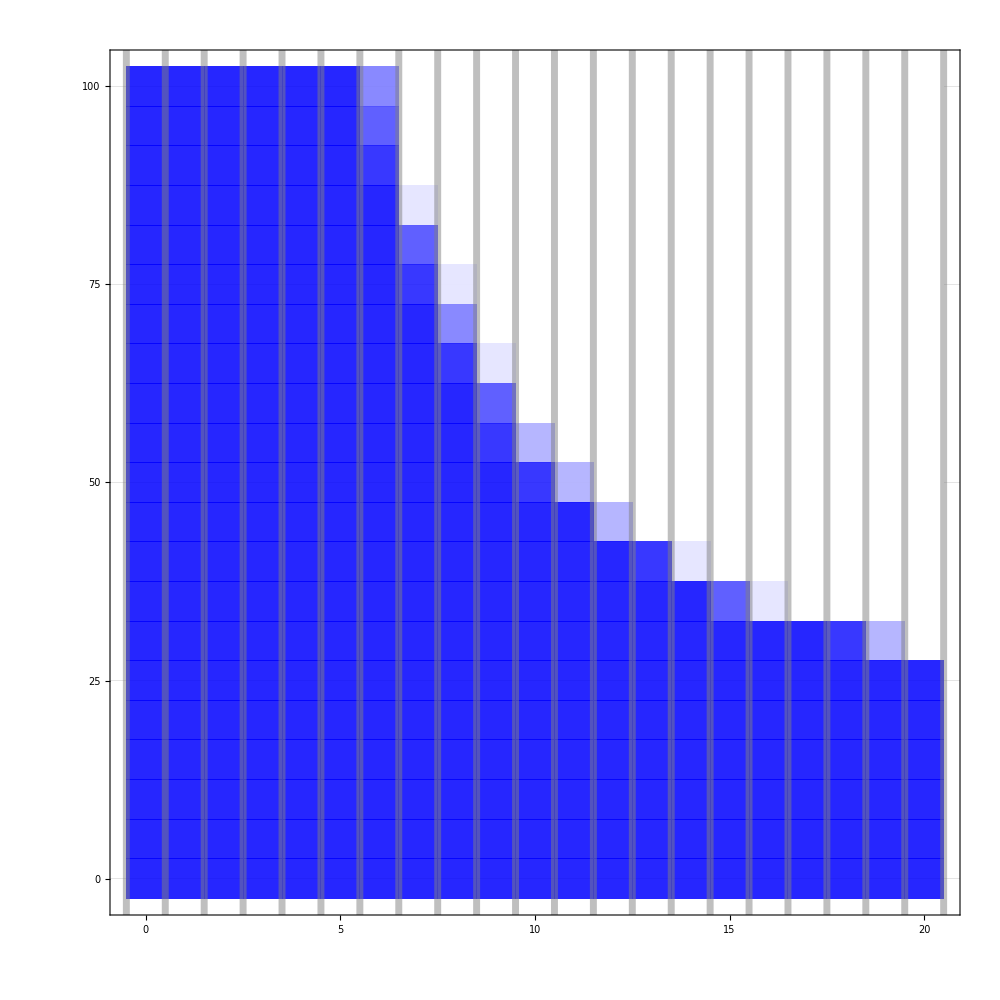

./images/WRYM.png

```mathematica
cf1=(Blend[{Directive[{hexToRGB["#ffffff"],Opacity[1]}],Directive[{RGBColor[0, 0, 1],Opacity[.85]}]},#1]&);
experiment="WRYM";
day=timeRange[[2]];
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import[experiment<>".csv"]];
x=If[(StringTake[experiment,{2}]=="X"),0,1];
filtered=If[
(StringTake[experiment,{1}]=="T"),
Cases[flattenedData,{a_,b_,day,c_}->{a,b,x-(x-c)/popsRatio}],
Cases[flattenedData,{a_,b_,day,c_}->{a,b,x-(x-(1-c))/popsRatio}]
];
{firstCol,firstRow}=ConstantArray[x,2];
contour=ListContourPlot[
Flatten[{
filtered,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[firstRow,flattenedData[[All,2]]//DeleteDuplicates//Length]
}]},1]
,ColorFunction->cf1
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025},{filtered[[All,3]]//Min,filtered[[All,3]]//Max}}
,PlotRangePadding->0
]
Export["./images/"<>experiment<>".png",contour,ImageResolution->500]
```

Response Surface: Fixation/Remediation for Two Nodes

```mathematica
cf1=(Blend[{Directive[{hexToRGB["#ffffff"],Opacity[1]}],Directive[{RGBColor[0, 0, 1],Opacity[.85]}]},#1]&);
Table[
day=timeRange[[2]];
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import[experiment<>".csv"]];
x=If[( Length[StringCases[experiment,_~~"Rem"~~_]]<1),0,1];
filtered=If[
(StringTake[experiment,{1}]=="T"),
Cases[flattenedData,{a_,b_,day,c_}->{a,b,x-(x-c)/popsRatio}],
Cases[flattenedData,{a_,b_,day,c_}->{a,b,x-(x-(1-c))/popsRatio}]
];
{firstCol,firstRow}=ConstantArray[x,2];
contour=ListContourPlot[
Flatten[{
{#[[1]],#[[2]],If[#[[3]]>1,1,If[#[[3]]<0,0,#[[3]]]]}&/@filtered,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length]
}],
Transpose[{
flattenedData[[All,1]]//DeleteDuplicates,
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length],
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length]
}]
},1]
,ColorFunction->cf1
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025},{0,1}}
,PlotRangePadding->0
];
Export["./images/"<>experiment<>".png",contour,ImageResolution->500];
Print[experiment];
,{experiment,experimentsList}]
```

Part::partw: Part 4 of {3.,0.25,0.} does not exist.

Part::partw: Part 4 of {19.,0.45,-0.00074} does not exist.

Part::partw: Part 4 of {20.,0.9,0.00032} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

Response Surface: Sensitivity for Two Nodes

```mathematica
cf2=(Blend[{{-1,Directive[RGBColor[0.0006103608758678569, 0., 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 0.9850156404974442],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#1]&);
Table[
day=timeRange[[2]];
x=If[( Length[StringCases[experiment,_~~"Rem"~~_]]<1),0,1];
{firstCol,firstRow}=ConstantArray[x,2];
flattenedData={#[[1]],#[[2]]*100,#[[3]]}&/@ToExpression[Import[experiment<>".csv"]];
contour=ListDensityPlot[
Flatten[{
{#[[1]],#[[2]],Chop[If[#[[3]]>1,1,If[#[[3]]<0,0,#[[3]]]],10^-10]}&/@flattenedData,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]
}]}
,1]
,ColorFunction->cf2
,ColorFunctionScaling->False
,ClippingStyle->White
,GridLines->{Range[-.5,20.5,1],Range[-102.5,100.5,5]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
,FrameTicks->{{{#,ToString[#*1//Round]}&/@Range[0,100,25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-2.5,102.5},{-1,1}}
,PlotRangePadding->0
];
(*Print[{#//Min,#//Mean,#//Max}&/@{flattenedData[[All,3]]}];*)
Export["./images/"<>experiment<>".png",contour,ImageResolution->500];
Print[experiment];
,{experiment,experimentsList}];
```

Translocations

TranslocationsRemediation

UDMel

UDMelRemediation

Wolbachia

WolbachiaRemediation

{Null,Null,Null,Null,Null,Null}

Response Surface: Batch Migration for Two Nodes

```mathematica
cf3=(Blend[{Directive[{hexToRGB["#ffffff"],Opacity[1]}],Directive[{RGBColor[1, 0, 0.5],Opacity[.85]}]},#1]&);
Table[
day=timeRange[[2]];
flattenedData={#[[1]],#[[2]]*10,Round[#[[3]]],#[[4]]}&/@ToExpression[Import[experiment<>".csv"]];
x=If[( Length[StringCases[experiment,_~~"Rem"~~_]]<1),0,1];
{firstCol,firstRow}=ConstantArray[x,2];
filtered=If[
(StringTake[experiment,{1}]=="T"),
Cases[flattenedData,{a_,b_,day,c_}->{a,b,x-(x-c)/popsRatio}],
Cases[flattenedData,{a_,b_,day,c_}->{a,b,x-(x-(1-c))/popsRatio}]
];
{firstCol,firstRow}=ConstantArray[x,2];
contour=ListContourPlot[
Flatten[{
{#[[1]],#[[2]],If[#[[3]]>1,1,If[#[[3]]<0,0,#[[3]]]]}&/@filtered,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length]
}],
Transpose[{
flattenedData[[All,1]]//DeleteDuplicates,
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length],
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length]
}]
},1]
,ColorFunction->cf3
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,.26,.01]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.05],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.005,.255},{0,1}}
,PlotRangePadding->0
];
Export["./images/"<>experiment<>".png",contour,ImageResolution->500];
Print[experiment];
,{experiment,experimentsList}];
```

Translocations_Batch_0010

Translocations_Batch_0020

Translocations_Batch_0100

Translocations_Batch_0200

Translocations_Batch_1000

Translocations_Batch_2000

Response Surface: Fixation/Remediation for One Node

```mathematica
cf1=(Blend[{Directive[{hexToRGB["#ffffff"],Opacity[1]}],Directive[{RGBColor[0, 0, 1],Opacity[.85]}]},#1]&);
Table[
day=timeRange[[2]];
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import[experiment<>".csv"]];
x=If[( Length[StringCases[experiment,_~~"R"~~_]]<1),0,1];
filtered=If[
(StringTake[experiment,{1}]=="T"),
Cases[flattenedData,{a_,b_,day,c_}->{a,b,x-(x-c)/1}],
Cases[flattenedData,{a_,b_,day,c_}->{a,b,x-(x-(1-c))/1}]
];
{firstCol,firstRow}=ConstantArray[x,2];
contour=ListContourPlot[
Flatten[{
{#[[1]],#[[2]],If[#[[3]]>1,1,If[#[[3]]<0,0,#[[3]]]]}&/@filtered,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length]
}],
Transpose[{
flattenedData[[All,1]]//DeleteDuplicates,
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length],
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length]
}]
},1]
,ColorFunction->cf1
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025},{0,1}}
,PlotRangePadding->0
];
Export["./images/"<>experiment<>".png",contour,ImageResolution->500];
Print[experiment];
,{experiment,experimentsList}]
```

TRYK

TXYK

URYK

UXYK

WRYM

WXYM

Response Surface (Sensitivity)

## Single Experiment

```mathematica
day=999;
experimentString="UXSA_200";
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import["./"<>experimentString<>".csv"]];
filtered=Cases[flattenedData,{a_,b_,day,c_}->{a,b,1-c}];
{firstCol,firstRow}=ConstantArray[0,2];
contour=ListDensityPlot[
Flatten[{
filtered,
Transpose[{ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[firstRow,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{0,Directive[RGBColor[1, 1, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 0.5],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025}}
,PlotRangePadding->0
]
Export["./images/"<>experimentString<>".pdf",contour,ImageSize->1000]
```

## Batch Experiment

```mathematica
expIDS={"T","U"};
expIDN=Flatten[{("XSA_"<>#),("RSA_"<>#)}&/@{"001","002","010","020","100","200"}];
expStrings=Table[(i<>#)&/@expIDN,{i,expIDS}]
```

```mathematica
Table[
Table[
experimentString=expStrings[[i,j]];
(**)
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import["./"<>experimentString<>".csv"]];
filtered=Cases[flattenedData,{a_,b_,day,c_}->{a,b,c}];
filtered=If[i==1,filtered,{#[[1]],#[[2]],1-#[[3]]}&/@filtered];
{firstCol,firstRow}=If[(i==1)&&(StringTake[experimentString,{2}]=="R"),ConstantArray[0,2],ConstantArray[1,2]];
{firstCol,firstRow}=If[(i==2)&&(StringTake[experimentString,{2}]=="X"),ConstantArray[0,2],ConstantArray[1,2]];
(**)
contour=ListDensityPlot[
Flatten[{
filtered,
Transpose[{ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[firstRow,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{0,Directive[RGBColor[1, 1, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 0.5],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025}}
,PlotRangePadding->0
];
Export["./imagesFinal/SA_N_"<>experimentString<>".pdf",contour,ImageSize->1000]
,{j,1,Length[expStrings[[i]]]}]
,{i,1,2}]
```

Response Surface (Sensitivity Difference)

## Single Experiment

```mathematica
experimentString="UXSA_0002Diff";
{firstCol,firstRow}=ConstantArray[0,2];
flattenedData=Chop[Import["./"<>experimentString<>".csv"],10^-2];
{flattenedData[[All,3]]//Max,flattenedData//Min}
flattenedData[[All,3]]//Sort;
dominant=If[Total[flattenedData[[All,3]]]<0,-1,1];
flattenedData={#[[1]],#[[2]]*10,If[#[[3]]<0,#[[3]],dominant*(#[[3]])]}&/@flattenedData;
```

{0.17087,-0.05866}

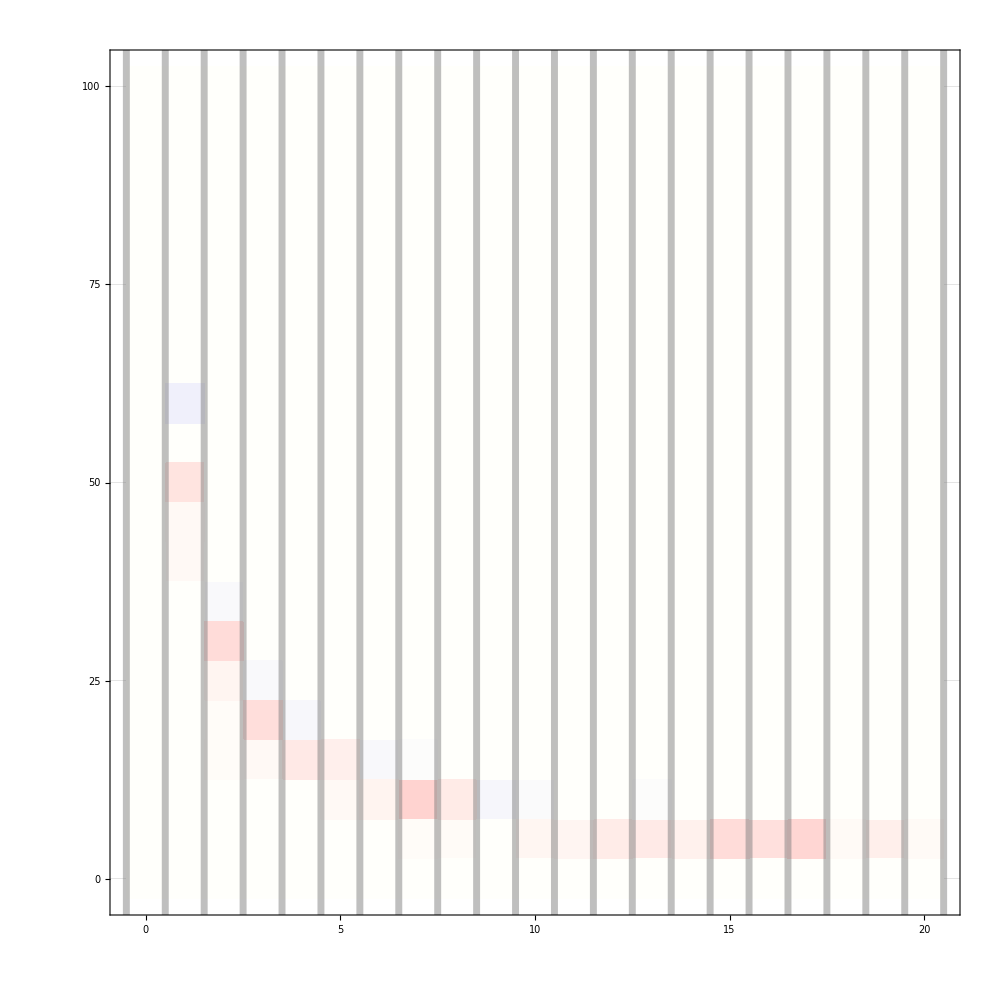

./images/UXSA_0002Diff.pdf

```mathematica
contour=ListDensityPlot[Flatten[{flattenedData,Transpose[{ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{-1,Directive[RGBColor[0.0006103608758678569, 0., 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 0.9850156404974442],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,ClippingStyle->Black
,GridLines->{Range[-.5,20.5,1],Range[-102.5,100.5,5]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*1//Round]}&/@Range[0,100,25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-2.5,102.5},{-1,1}}
,PlotRangePadding->0
]
Export["./images/"<>experimentString<>".pdf",contour,ImageSize->1000]
```

## Batch Experiment

```mathematica
expIDS={"T","U"};
expIDN=Flatten[{("XSA_"<>#<>"Diff"),("RSA_"<>#<>"Diff")}&/@{"001","002","010","020","100","200"}];
expStrings=Table[(i<>#)&/@expIDN,{i,expIDS}]
```

```mathematica
Table[
Table[
experimentString=expStrings[[i,j]];
{firstCol,firstRow}=ConstantArray[0,2];
flattenedData=Chop[Import["./"<>experimentString<>".csv"],10^-2];
dominant=If[Total[flattenedData[[All,3]]]<0,-1,1];
flattenedData={#[[1]],#[[2]],If[#[[3]]<0,#[[3]],1*(#[[3]])]}&/@flattenedData;
flattenedData=If[i==1,flattenedData,{#[[1]],#[[2]],-1*#[[3]]}&/@flattenedData];
(**)
contour=ListDensityPlot[Flatten[{flattenedData,Transpose[{ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{-1,Directive[RGBColor[0.0006103608758678569, 0., 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 0.9850156404974442],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,ClippingStyle->Black
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025},{-1,1}}
,PlotRangePadding->0
];
Export["./imagesFinal/SA_D_"<>experimentString<>".pdf",contour,ImageSize->1000]
,{j,1,Length[expStrings[[i]]]}]
,{i,1,2}]
```

Response Surface (Batch Migration Sensitivity)

```mathematica
day=1093;
experimentString="UBSA_200Diff";
multiplier=1;
flattenedData=Chop[Import["./"<>experimentString<>".csv"],10^-2];
(*{flattenedData[[All,3]]//Max,flattenedData//Min}
flattenedData[[All,3]]//Sort;
dominant=If[Total[flattenedData[[All,3]]]<0,-1,1];
flattenedData={#[[1]],#[[2]]*multiplier,2*If[#[[3]]<0,#[[3]],dominant*(#[[3]])]}&/@flattenedData;*)
ListDensityPlot[flattenedData,InterpolationOrder->0];
flattenedData[[All,3]]//Sort;
```

```mathematica
contour=ListDensityPlot[Flatten[{flattenedData,Transpose[{flattenedData[[All,1]]//DeleteDuplicates,ConstantArray[0,flattenedData[[All,1]]//DeleteDuplicates//Length],ConstantArray[0,flattenedData[[All,1]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{-1,Directive[RGBColor[0.0006103608758678569, 0., 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 0.9850156404974442],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,GridLines->{Range[-.5,41,1],Range[-.005,.25,.01]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,.25,.05],None},{Range[0,40,10],None}}
,FrameTicksStyle->Directive[Bold,65]
,PlotLegends->None
,PlotRange->{{-.5,20.5},{-.005,.255},{-1,1}}
,PlotRangePadding->0
]
Export["./images/"<>experimentString<>".pdf",contour,ImageSize->1000]
```

Timing: Fixation/Remediation for One Node

```mathematica
expString="TXYK";
flattenedData=Import[Directory[]<>"/"<>expString<>".csv"];
```

## One

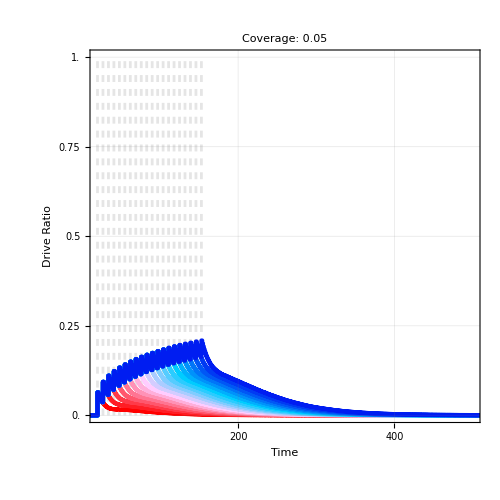

```mathematica
coverage=.05;
If[
(StringTake[expString,{1}]=="T"),
probed=Cases[flattenedData,{#,coverage,_,c_}->c]&/@(flattenedData[[All,1]]//DeleteDuplicates);,
probed=Cases[flattenedData,{#,coverage,_,c_}->1-c]&/@(flattenedData[[All,1]]//DeleteDuplicates);
];
releasesSort=Ordering[flattenedData[[All,1]]//DeleteDuplicates];
plot=ListLinePlot[probed[[releasesSort]]
,AspectRatio->1
,Frame->True
,FrameLabel->(Style[#,50]&/@{"Time","Drive Ratio"})
,FrameStyle->Directive[Thickness[.0025],Gray]
,FrameTicks->{{Range[0,1,.25],None},{Flatten[{Range[0,1000,200]}],None}}
,FrameTicksStyle->20
,GridLines->{Range[0,1000,200],Range[0,1,.25]}
,GridLinesStyle->Directive[Gray,Thick,Opacity[.2]]
,ImageSize->500
,InterpolationOrder->0
,PlotLabel->Style["Coverage: "<>ToString[coverage],40]
,PlotRange->{{20,500},{0,1}}
,PlotStyle->({
Thickness[.006],Blend[{{1,Directive[RGBColor[0.0006103608758678569, 0., 0.9347219043259327],Opacity[1.]]},{.35,Directive[RGBColor[1, 0.8, 1],Opacity[1]]},{.65,Directive[RGBColor[0, 0.8, 1],Opacity[1]]},{0,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]}&/@Range[0,1,.05])
,Prolog->Flatten[{Opacity[.1],Dashed,Thickness[.004],Line[{{#,0},{#,1}}]&/@(Range[0,7*20-1,1*7]+20)}]
]
```

```mathematica
lastRelease=(Range[0,7*20-1,1*7]+20)//Last
probed[[10]]//Last
```

```mathematica
range=Range[1,20,1];
blends=Blend[{{1,Directive[RGBColor[0.0006103608758678569, 0., 0.9347219043259327],Opacity[1.]]},{.35,Directive[RGBColor[1, 0.8, 1],Opacity[1]]},{.65,Directive[RGBColor[0, 0.8, 1],Opacity[1]]},{0,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]&/@Range[.05,1,.05];
colorScale=Transpose[{
Reverse[ImageResize[Rasterize[#]//ImageCrop,50]&/@blends],
Reverse[Style[ToString[#],35]&/@range]
}]//Grid;
Export["./images/CoverageSweeps/colorScale.pdf",colorScale]
```

./images/CoverageSweeps/colorScale.pdf

## Batch

```mathematica
Table[
expStringSample=j;
x=If[( Length[StringCases[expStringSample,_~~"R"~~_]]<1),0,1];
dID=(StringTake[expStringSample,{1}]=="T");
flattenedData=Import[Directory[]<>"/"<>expStringSample<>".csv"];
Table[
coverage=i;
If[dID,
probed=Cases[flattenedData,{#,coverage,_,c_}->Abs[x-(x-c)/1]]&/@(flattenedData[[All,1]]//DeleteDuplicates);,
probed=Cases[flattenedData,{#,coverage,_,c_}->Abs[x-(x-(1-c))/1]]&/@(flattenedData[[All,1]]//DeleteDuplicates);
];
releasesSort=Ordering[flattenedData[[All,1]]//DeleteDuplicates];
plot=ListLinePlot[probed[[releasesSort]]
,AspectRatio->1
,Frame->True
(*,FrameLabel->(Style[#,60]&/@{"Time","Drive Ratio"})*)
,FrameStyle->Directive[Thickness[.0075],Gray,50]
,FrameTicks->None
,FrameTicksStyle->20
,GridLines->{Range[0,1000,200],Range[0,1,.25]}
,GridLinesStyle->Directive[Gray,Thick,Opacity[.2]]
,ImageSize->500
,InterpolationOrder->1
,PlotRange->{{20,500},{0,1}}
,PlotStyle->({
Thickness[.006],Blend[{{1,Directive[RGBColor[0.0006103608758678569, 0., 0.9347219043259327],Opacity[1.]]},{.35,Directive[RGBColor[1, 0.8, 1],Opacity[1]]},{.65,Directive[RGBColor[0, 0.8, 1],Opacity[1]]},{0,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]}&/@Range[0,1,.05])
,Prolog->Flatten[{Opacity[.25],Thickness[.001],Line[{{#,0},{#,1}}]&/@(Range[0,7*20-1,1*7]+20)}]
];
Export["./images/CoverageSweeps/"<>expStringSample<>StringPadLeft[ToString[coverage*100],4,"0"]<>"png",plot,ImageSize->1000]
,{i,flattenedData[[All,2]]//DeleteDuplicates}];
,{j,experimentsList}]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

Timing

```mathematica
experimentString=experimentString="E_02_05_0001_0050";
flattenedData=Import["./"<>experimentString<>".csv"][[2;;All]];
```

```mathematica
i=1;
releasesNumber=flattenedData[[All,1]]//DeleteDuplicates
probed=Cases[flattenedData,{#,coverage,_,c_}->1-c]&/@releasesNumber
```

{1}

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0639793,0.0580501,0.0527396,0.0477454,0.043314,0.0392881,0.0356279,0.0323526,0.0331344,0.0333808,0.0331714,0.0328252,0.0326549,0.0323984,0.0318251,0.0311635,0.030858,0.0305712,0.0303991,0.0303394,0.0302008,0.0300205,0.0298387,0.0296138,0.029488,0.0296428,0.0295802,0.0295565,0.0295786,0.0296163,0.0294563,0.0294005,0.0295291,0.0296449,0.0297418,0.0297154,0.0296582,0.0295959,0.0295726,0.0295754,0.0295786,0.0294503,0.0293881,0.0294426,0.0294529,0.0294824,0.0294548,0.02965,0.0295929,0.029612,0.0296507,0.0296145,0.0295833,0.0296943,0.0296091,0.0297487,0.0298199,0.0298124,0.0297897,0.0299895,0.0300358,0.0300101,0.0300439,0.0301493,0.0301894,0.030103,0.0301122,0.0301757,0.0302569,0.0303083,0.0302904,0.0303824,0.0303733,0.030265,0.0303342,0.0304318,0.0304007,0.0303547,0.0302731,0.0302937,0.030236,0.0303496,0.0304563,0.0306093,0.0306316,0.0308252,0.0310786,0.0309979,0.0310851,0.0310922,0.0311562,0.0311974,0.0311178,0.0311951,0.031126,0.0311991,0.0312448,0.0314748,0.031465,0.0315218,0.0317119,0.0318011,0.0316704,0.0314745,0.0314605,0.0316565,0.0317214,0.0318887,0.0317936,0.0318845,0.0318121,0.0318966,0.0318427,0.0318196,0.0318536,0.0320627,0.0321658,0.0321403,0.0321452,0.0321877,0.0321782,0.0322506,0.0323344,0.0322374,0.0322802,0.0322859,0.0322024,0.0322553,0.032206,0.0321285,0.032134,0.0320832,0.0321148,0.0323237,0.032504,0.0324971,0.0325108,0.0325139,0.0325052,0.0327306,0.0327765,0.0327219,0.0326181,0.0325892,0.0326411,0.0326974,0.0326671,0.0327208,0.0328066,0.0326903,0.0326536,0.0327321,0.0328089,0.0329731,0.0330295,0.0329727,0.032987,0.0329709,0.0331225,0.0332249,0.0331839,0.0331919,0.0332376,0.0332968,0.0333483,0.0333115,0.0332612,0.0333368,0.0333426,0.0333045,0.0333232,0.0332731,0.0332859,0.0333737,0.0332922,0.0333645,0.0335734,0.0338022,0.0336483,0.0335271,0.0335723,0.0338394,0.0339741,0.0339367,0.033726,0.0337635,0.0337062,0.0337651,0.0338042,0.0338318,0.0339102,0.0338258,0.0339581,0.0340206,0.0340679,0.0340282,0.0339897,0.0339993,0.0339123,0.0338908,0.0339643,0.0340811,0.0340512,0.034108,0.0340622,0.03425,0.034242,0.0343787,0.0343334,0.0342377,0.0342772,0.0343074,0.0344722,0.0345401,0.0347759,0.0349066,0.0349995,0.0350248,0.0347749,0.0349545,0.0348929,0.0349165,0.0349497,0.034876,0.0349452,0.0349732,0.0350815,0.0351195,0.035297,0.0354006,0.0353487,0.0352931,0.035324,0.0353596,0.0352695,0.0352604,0.0352421,0.0352857,0.0352796,0.0354257,0.0354654,0.0356901,0.0355443,0.0354581,0.0355063,0.0354863,0.0355158,0.0354382,0.0352238,0.0353605,0.0352498,0.035222,0.0354696,0.0356054,0.0355118,0.035646,0.0357375,0.0358063,0.0359169,0.0359143,0.0360308,0.0359253,0.0360749,0.0361516,0.0363209,0.0364689,0.0364127,0.0364592,0.0366537,0.0365884,0.0364655,0.0366311,0.0367549,0.0367815,0.0369162,0.0371152,0.0372329,0.0373254,0.0373861,0.0375608,0.037641,0.0376924,0.0376374,0.0377422,0.03773,0.0377875,0.0378888,0.0380535,0.0380552,0.0382044,0.0383603,0.0384151,0.038729,0.0388367,0.0389368,0.0390677,0.0390989,0.0392332,0.0392945,0.0394329,0.0395266,0.0395649,0.0397117,0.0398039,0.0397902,0.039717,0.0398491,0.0400661,0.0402394,0.0401798,0.0402644,0.0403594,0.0407499,0.0406163,0.0407909,0.0408506,0.0409956,0.0411766,0.0412936,0.0414553,0.0414517,0.0416692,0.0416353,0.0417848,0.0420262,0.0418838,0.0420358,0.0419741,0.0421294,0.0420703,0.0420494,0.0421735,0.0422478,0.0422873,0.042374,0.0428018,0.0428866,0.0429872,0.0428601,0.0430388,0.0431647,0.0431323,0.0433497,0.0434155,0.0435698,0.0438892,0.0439289,0.0440918,0.0442718,0.0443244,0.0444445,0.0444738,0.0445012,0.0444662,0.0447096,0.0449073,0.0450752,0.0451555,0.0452746,0.0453502,0.0454723,0.0455009,0.0455795,0.045788,0.0459743,0.0458411,0.0456795,0.0458088,0.0460187,0.0463367,0.0463196,0.0466135,0.0467524,0.0468235,0.0467814,0.0468928,0.0468884,0.0470058,0.0468032,0.0470927,0.0470566,0.0471826,0.0473135,0.0475008,0.0477189,0.0478773,0.0479166,0.0481904,0.0482807,0.0484489,0.0486086,0.0484557,0.0485752,0.0488726,0.049045,0.0491596,0.0492759,0.0493749,0.0494326,0.0495556,0.0496655,0.0495629,0.0496257,0.0499564,0.0503556,0.0502373,0.0503778,0.0505911,0.0508151,0.0507291,0.0509052,0.0512108,0.0512207,0.0516,0.0518545,0.0519457,0.0519898,0.0522557,0.0524252,0.0528315,0.0529882,0.0529413,0.0531808,0.0532766,0.0534344,0.0537212,0.0539611,0.0541881,0.0542183,0.0544039,0.0543396,0.0544166,0.0546917,0.0547451,0.0550215,0.055339,0.0554701,0.0558016,0.0559502,0.055951,0.0559511,0.0561406,0.0561867,0.0564582,0.0566827,0.0568453,0.0569088,0.0572398,0.0573317,0.0575177,0.0574401,0.057541,0.0576265,0.0577609,0.057875,0.0578611,0.0584538,0.0586669,0.0589368,0.0590601,0.0592179,0.0594357,0.0596201,0.059638,0.0600081,0.0600546,0.0604169,0.0607352,0.0611013,0.0614028,0.0616427,0.0617327,0.0618169,0.0619982,0.0622366,0.0623809,0.0626313,0.0625791,0.0626752,0.0629534,0.0631416,0.0631829,0.0633178,0.0632996,0.063543,0.0636946,0.0641294,0.0644342,0.0648359,0.0651033,0.0655145,0.0656169,0.0658283,0.0660486,0.0661041,0.0663627,0.0663328,0.066555,0.0666891,0.0668676,0.0671242,0.0675555,0.0678244,0.0681567,0.0684673,0.0686249,0.068914,0.0692091,0.06958,0.0697259,0.0700636,0.0702346,0.0704341,0.0707612,0.0712994,0.0716059,0.0717362,0.0719126,0.0721294,0.0723755,0.0726719,0.0729272,0.0732073,0.0735446,0.0736512,0.0739988,0.0740901,0.0744923,0.0749172,0.0749935,0.0751052,0.0754412,0.0756766,0.075921,0.0763866,0.0765292,0.0768366,0.0773175,0.0776068,0.077925,0.0779862,0.0782379,0.0785852,0.0790415,0.0792342,0.0795475,0.0797983,0.0799084,0.0802304,0.080453,0.0809055,0.0809141,0.0811236,0.0813919,0.0812497,0.0814948,0.0816918,0.0819589,0.0820428,0.082859,0.0830238,0.083251,0.0834855,0.0837533,0.0843223,0.0845257,0.0847805,0.0853156,0.0853838,0.0857583,0.0859837,0.0864082,0.0869156,0.0871804,0.0874815,0.0878423,0.0878397,0.0879574,0.0882677,0.0885743,0.0887965,0.0892605,0.0893938,0.0895399,0.0896366,0.090153,0.0899849,0.0904392,0.0909447,0.0913605,0.0916234,0.0918973,0.0925534,0.0927753,0.0930983,0.0934983,0.0935964,0.0938075,0.094415,0.0946175,0.0950336,0.0953607,0.0957233,0.0963117,0.0968152,0.0971637,0.0972093,0.0976651,0.0979856,0.0983399,0.098931,0.0991558,0.0994766,0.0994956,0.099877,0.100131,0.100392,0.100579,0.101129,0.101841,0.102535,0.102994,0.103185,0.103745,0.104302,0.104303,0.104555,0.104924,0.105466,0.105642,0.10633,0.106752,0.107386,0.107872,0.108021,0.10826,0.108682,0.109269,0.109867,0.110498,0.110952,0.111608,0.112055,0.112784,0.113046,0.113249,0.113969,0.114556,0.114947,0.115382,0.11564,0.11611,0.11656,0.116873,0.117461,0.117971,0.118185,0.118789,0.119492,0.119741,0.12025,0.120721,0.121513,0.121696,0.122096,0.122573,0.123177,0.123517,0.124089,0.124641,0.125284,0.125791,0.126338,0.127043,0.127539,0.127786,0.128046,0.128294,0.128576,0.128949,0.129376,0.130377,0.130974,0.131669,0.132511,0.132819,0.133563,0.133931,0.13467,0.134847,0.135633,0.13637,0.13684,0.13746,0.137959,0.138039,0.138616,0.139104,0.140078,0.140883,0.141411,0.142152,0.143146,0.143745,0.144668,0.145115,0.145586,0.146093,0.146559,0.147261,0.148054,0.148641,0.149003,0.149479,0.149991,0.150485,0.151379,0.151764,0.152395,0.153384,0.15381,0.154421,0.154912,0.155412,0.155867,0.156689,0.157632,0.158217,0.158965,0.159667,0.160252,0.161059,0.161762,0.162433,0.162868,0.163373,0.163897,0.164601,0.165269,0.166449,0.167383,0.168382,0.168733,0.169075,0.169813,0.17042,0.171091,0.171815,0.171786,0.172723,0.17389,0.174581,0.175308,0.175813,0.177083,0.177949,0.178655,0.179001,0.180264,0.181382,0.181931,0.182383,0.183247,0.183881,0.184398,0.184904,0.185957,0.187044,0.187662,0.188296,0.188766,0.189563,0.190459,0.191089,0.191399,0.192256,0.193172,0.193886,0.195124,0.195942,0.196499,0.197244,0.197711,0.198327,0.199291,0.200026,0.200839,0.201202,0.202171,0.202989,0.203959,0.204626,0.205406,0.20612,0.206729,0.207502,0.208206,0.20885,0.209905,0.210866,0.211828,0.212634,0.212961,0.213741,0.214482,0.215302,0.216158,0.216871,0.217864,0.219188,0.21997,0.22042,0.221241,0.222195,0.222814,0.223595,0.224954,0.225938,0.227192,0.228053,0.229435,0.230026,0.23083,0.231844,0.233248,0.234181,0.234885,0.23585,0.237228,0.238169,0.239115,0.23989,0.240749,0.241917,0.243104,0.24372,0.244311,0.245123,0.24629,0.247173,0.248499,0.249407,0.250132,0.251265,0.25244,0.2534,0.25421,0.255385,0.256385,0.256997,0.257686,0.258488,0.259689,0.260541,0.261495,0.262581,0.263951,0.264953,0.265693,0.267231,0.26803,0.268963,0.26972,0.270612,0.271346,0.272854,0.273902,0.274674,0.275462,0.276284,0.277294,0.27854,0.278813,0.279456,0.280437,0.281566,0.282473,0.283501,0.284864,0.285712,0.286669,0.287702,0.288546,0.290073,0.291348,0.292394,0.292968,0.294518,0.295768,0.296377,0.297707,0.29919,0.299947,0.300782,0.301616,0.302881,0.304083,0.305033,0.305731,0.306781,0.307865,0.308615,0.309895,0.310789,0.312058,0.313062,0.314285,0.315692,0.316883,0.318234,0.319233,0.320331,0.32155,0.322314,0.323239,0.324618,0.325791,0.327208,0.327622,0.329034,0.330739,0.331797,0.332582,0.334076,0.334758,0.335773,0.337055,0.337879,0.338902,0.340113,0.341416,0.342506,0.34334,0.344652,0.345791,0.34679,0.347823,0.348781,0.350146,0.351456,0.35255,0.35363,0.354799,0.356048,0.357271,0.3583,0.359473,0.36058,0.361503,0.362048,0.362854,0.364272,0.36499,0.366319,0.366952,0.368629,0.370102,0.37119,0.371907,0.373285,0.374003,0.375159,0.375945,0.377087,0.377779,0.378645,0.379772,0.381027,0.382079,0.382977,0.384353,0.385385,0.386792,0.388425,0.390074,0.391123,0.392193,0.39311,0.394112,0.395398,0.396351,0.396819,0.398364,0.399369,0.400469,0.401734,0.402645,0.403831,0.404592,0.405436,0.406574,0.408338,0.409604,0.410507,0.412146,0.413717,0.414777,0.415932,0.416966,0.417596,0.418532,0.419387,0.420941,0.422417,0.423218,0.424371,0.425686,0.426732,0.428135,0.429336,0.431229,0.432228,0.433569,0.434707,0.436127,0.437268,0.438113,0.439039,0.439662,0.44102,0.442412,0.443135,0.444741,0.446339,0.447641,0.448426,0.449628,0.450819,0.451872,0.452895,0.454462,0.455305,0.456375,0.457492,0.458554,0.459549,0.460411,0.461493,0.462777,0.46367,0.46506,0.466531,0.467428,0.468111,0.469357,0.47052,0.471728,0.473233,0.474544,0.475406,0.476942,0.478301,0.479756,0.480571,0.481391,0.482909,0.484391,0.485876,0.486848,0.487979,0.489639,0.491501,0.492648,0.493991,0.494615,0.495371,0.496058,0.496745,0.498495,0.499983,0.501285,0.502274,0.503931,0.504777,0.506126}}

```mathematica
Table[
coverage=i;
releasesNumber=flattenedData[[All,1]]//DeleteDuplicates;
probed=Cases[flattenedData,{#,coverage,_,c_}->1-c]&/@releasesNumber;
plot=ListLinePlot[probed
,AspectRatio->1
,Filling->Prepend[(#->{#+1})&/@Range[1,Length[probed]-1],1->1]
,FillingStyle->Opacity[0]
,Frame->True
,FrameStyle->Directive[Thickness[.0075],Gray,50]
,FrameTicks->None(*{{{#,StringPadRight[ToString[#],4,"0"]}&/@Range[0,1,.5],None},{Flatten[{Range[0,1000,200]}],None}}*)
,FrameTicksStyle->30
,GridLines->{Range[0,1000,200],Range[0,1,.25]}
,GridLinesStyle->Directive[Gray,Thick,Opacity[.2]]
,ImageSize->1000
,InterpolationOrder->0
,PlotRange->{{9*20,1000},{0,1}}
,PlotStyle->({Thickness[.005],Blend[{{0,Directive[RGBColor[1, 0.5, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 1],Opacity[1]]}},#]}&/@Range[0,1,.05])
,Prolog->Flatten[{Opacity[.2],Dashed,Thickness[.001],Line[{{#,0},{#,1}}]&/@(Range[0,7*20-1,1*7]+20)}]
];
Export["./"<>experimentString<>"_"<>StringPadLeft[ToString[coverage*100//Round],4,"0"]<>".png",plot,ImageSize->1000]
,{i,flattenedData[[All,2]]//DeleteDuplicates}]
```

ListLinePlot::lpn: {{{1.,1.-1. Ratio}},{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

$Aborted

```mathematica
Line[{ConstantArray[0,probed[[2]]//Length],Range[1,probed[[2]]//Length],probed[[2]]}//Transpose]
```

```mathematica
Range[First[releasesNumber],Last[releasesNumber],4]
releasesNumber
```

```mathematica
two=Blend[{{0,Directive[RGBColor[1, 0.5, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 1],Opacity[1]]}},#]&/@Range[0,1,1]
SwatchLegend[two,{"1 release","20 releases"}]
```

```mathematica
BarLegend[{Blend[{{0,Directive[RGBColor[1, 0.5, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 1],Opacity[1]]}},#]&,{0,1}},20]
Export["swatch.pdf",%,ImageSize->1000]
```

```mathematica
(#->{#+1})&/@Range[2,10]
```

Legends

```mathematica
BarLegend[{(Blend[{{0,Directive[RGBColor[1, 1, 1],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0.5],Opacity[1]]}},#]&),{0,1}}]
Export["./images/colorScaleBatch.pdf",%,ImageSize->500]
BarLegend[{(Blend[{Directive[{hexToRGB["#ffffff"],Opacity[1]}],Directive[{RGBColor[0, 0, 1],Opacity[.85]}]},#1]&),{0,1}}]
Export["./images/colorScale.pdf",%,ImageSize->500]
BarLegend[{(Blend[{{0,Directive[RGBColor[1, 1, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 0.5],Opacity[1]]}},#]&),{0,1}}]
Export["./images/colorScaleSensitivity.pdf",%,ImageSize->500]
BarLegend[{Blend[{{-1,Directive[RGBColor[0.0006103608758678569, 0., 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 0.9850156404974442],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#1]&,{-1,1}}]
Export["./images/colorScaleSensitivity2.pdf",%,ImageSize->500]
```

./images/colorScaleBatch.pdf

./images/colorScale.pdf

./images/colorScaleSensitivity.pdf

./images/colorScaleSensitivity2.pdf

```mathematica
SwatchLegend[
{ColorData[{"DeepSeaColors",{0,1}}][0],ColorData[{"DeepSeaColors",{0,1}}][1]},
{"0% Drive","100% Drive"}
,LegendMarkerSize->50
,LabelStyle->50
]
Export["swatchFixation.pdf",%]
```

Resolution (Sensitivity Difference)

```mathematica
cf2=(Blend[{{-1,Directive[RGBColor[0.0006103608758678569, 0., 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 0.9850156404974442],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#1]&);
Table[
day=timeRange[[2]];
x=If[( Length[StringCases[experiment,_~~"R"~~_]]<1),0,1];
{firstCol,firstRow}=ConstantArray[x,2];
flattenedData={#[[1]],#[[2]]*100,#[[3]]}&/@ToExpression[Import[experiment<>".csv"]];
contour=ListDensityPlot[
Flatten[{
{#[[1]],#[[2]],Chop[#[[3]]]}&/@flattenedData,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]
}]}
,1]
,ColorFunction->cf2
,ColorFunctionScaling->False
,ClippingStyle->{RGBColor[0.0006103608758678569, 0., 1],RGBColor[1, 0, 0]}
,GridLines->{Range[-.5,20.5,1],Range[-102.5,100.5,5]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
,FrameTicks->{{{#,ToString[#*1//Round]}&/@Range[0,100,25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-2.5,102.5},{-1,1}}
,PlotRangePadding->0
];
(*Print[{#//Min,#//Mean,#//Max}&/@{flattenedData[[All,3]]}];*)
Export["./images/"<>experiment<>".png",contour,ImageResolution->500];
Print[experiment];
,{experiment,experimentsList}];
```

TR

TX

UR

UX

WR

WX